## PREAMBLE

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
```

x::shdw: Symbol x appears in multiple contexts {NumberTheory`,Global`}; definitions in context NumberTheory` may shadow or be shadowed by other definitions.

```mathematica
nCollatz[16]
```

{16,8,4,2,1}

```mathematica
nQuotientToNatural[20]
```

801

```mathematica
nNaturalToQuotient[801]
```

20

```mathematica
CoefficientList[Series[Zeta[x],{x,0,10}],x]//N
```

{-0.5,-0.918939,-1.00318,-1.00079,-0.999879,-1.,-1.,-1.,-1.,-1.,-1.}

```mathematica
Series[Zeta[x],{x,∞,6}]
Series[Zeta[x],{x,∞,6}]//Normal
Series[Zeta[x]^2,{x,∞,6}]//Normal//Expand
CoefficientList[Series[Zeta[x],{x,∞,9}]//Normal,x]
```

1+2^(-x+O[1/x]^7)+3^(-x+O[1/x]^7)+4^(-x+O[1/x]^7)+5^(-x+O[1/x]^7)+6^(-x+O[1/x]^7)

1+2^-x+3^-x+4^-x+5^-x+6^-x

1+2^(1-3 x)+2^(1-2 x)+2^(1-x)+2^(-2 x)+3^(-2 x)+2 3^-x+2^(1-3 x) 3^-x+2^(2-2 x) 3^-x+2^(2-x) 3^-x+4^(-2 x)+5^(-2 x)+2 5^-x+2^(1-2 x) 5^-x+2^(1-x) 5^-x+6^(-2 x)+2^(1-x) 9^-x+2 15^-x+2^(1-x) 15^-x

{1+2^(-3 x)+2^(-2 x)+2^-x+3^(-2 x)+3^-x+5^-x+6^-x+7^-x}

```mathematica
h[x_]:=x/Log[x]-2/Log[2]+Integrate[1/Log[t]^2,{t,0.01,x}]
```

```mathematica
LogIntegral[3.99]
h[3.99]//N
```

2.96037

Integrate::idiv: Integral of 1/Log[t]^2 does not converge on {0.01,3.99}.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.00494}. NIntegrate obtained 1.52056×10^6 and 1.51593×10^6 for the integral and error estimates.

1.52056×10^6

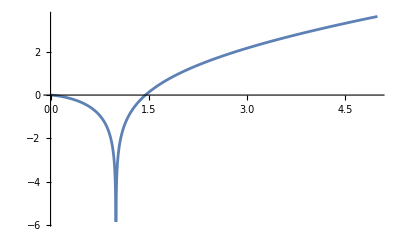

```mathematica
Plot[LogIntegral[x],{x,0,5}]
```

2001 | -0.9995
2002 | 1.0005
2003 | -0.999501
2004 | 1.0005
2005 | -0.999501
2006 | 1.0005
2007 | -0.999502
2008 | 1.0005
2009 | -0.999502
2010 | 1.0005
2011 | -0.999503

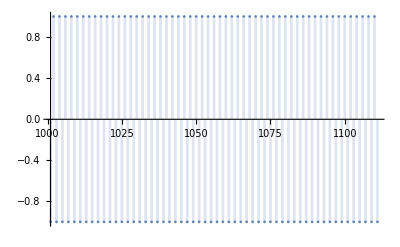

```mathematica
Table[{n,(-1)^n+1/n//N},{n,2001,2011}]//tf
DiscretePlot[(-1)^n+1/n,{n,1001,1111}]
```

```mathematica
D[ComplexExpand[z^2,z]/.{Re[z]:>x,Im[z]:>y},x]
D[ComplexExpand[z^2,z]/.{Re[z]:>x,Im[z]:>y},y]
```

2 x+2 ⅈ y

2 ⅈ x-2 y